```mathematica
L = 1;
F[x_]:= x^2
foddbas[x_]:=If[x>0,F[x],-F[-x]]
fodd[x_]:=foddbas[Mod[x,2*L,-L]]
B[n_]=Simplify[2/L ∫_0^L F[x]*Sin[n*Pi*x/L]ⅆx,Assumptions-> n∈Integers]
```

```mathematica
-(2 (2-2 (-1)^n+(-1)^n n^2 π^2))/(n^3 π^3)
```

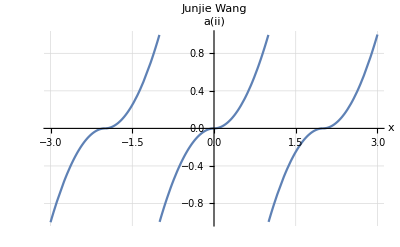

```mathematica
Plot[{Piecewise[{{x^2,0<x<1},{-x^2,-1<x<0},{(x-2)^2,2<x<3},{-(x-2)^2,1<x<2},{(x+2)^2,-2<x<-1},{-(x+2)^2,-3<x<-2}}]},{x,-3,3},

AxesLabel-> {"x","a(ii)"},
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

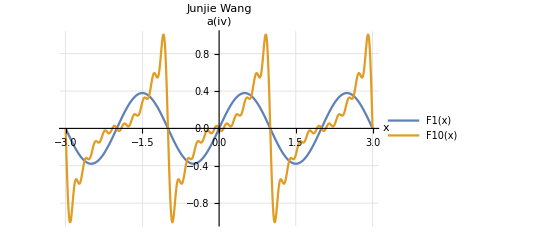

```mathematica
F1[x_]:={Sum[-(2 (2-2 (-1)^n+(-1)^n n^2 π^2))/(n^3 π^3)*Sin[n*Pi*x],{n,1,1}]}
F10[x_]:={Sum[-(2 (2-2 (-1)^n+(-1)^n n^2 π^2))/(n^3 π^3)*Sin[n*Pi*x],{n,1,10}]}
Plot[{F1[x],F10[x]},{x,-3,3},

AxesLabel-> {"x","a(iv)"},
PlotLegends->"Expressions",
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

```mathematica
L = 1;
F[x_]:= x-x^2
foddbas[x_]:=If[x>0,F[x],-F[-x]]
fodd[x_]:=foddbas[Mod[x,2*L,-L]]
B[n_]=Simplify[2/L ∫_0^L F[x]*Sin[n*Pi*x/L]ⅆx,Assumptions-> n∈Integers]
```

-((4 (-1+(-1)^n))/(n^3 π^3))

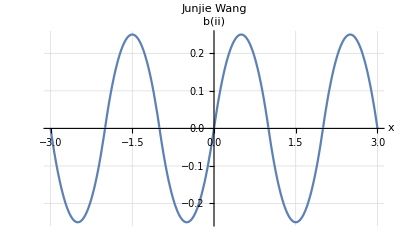

```mathematica
F[x_]:=x-x^2
Plot[{Piecewise[{{x-x^2,0<x<1},{-((x+1)-(x+1)^2),-1<x<0},{(x-2)-(x-2)^2,2<x<3},{-((x-1)-(x-1)^2),1<x<2},{(x+2)-(x+2)^2,-2<x<-1},{-((x+3)-(x+3)^2),-3<x<-2}}]},{x,-3,3},

AxesLabel-> {"x","b(ii)"},
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

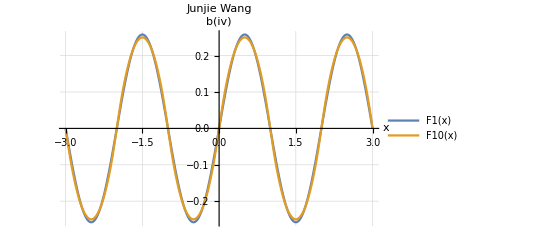

```mathematica
F1[x_]:={Sum[-((4 (-1+(-1)^n))/(n^3 π^3))*Sin[n*Pi*x],{n,1,1}]}
F10[x_]:={Sum[-((4 (-1+(-1)^n))/(n^3 π^3))*Sin[n*Pi*x],{n,1,10}]}
Plot[{F1[x],F10[x]},{x,-3,3},

AxesLabel-> {"x","b(iv)"},
PlotLegends->"Expressions",
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

Set::write: Tag Range in Range[If[x>0,F[x],F1[x]]] is Protected.

{(4 Sin[(n π)/2])/(n^2 π^2)}

Set::write: Tag Range in Range[If[x>0,F[x],F1[x]]] is Protected.

Syntax::tsntxi: "F[x_] := x, foddbas[x_] := If[0 < x < L/2, F[x], -F[-x]]" is incomplete; more input is needed.\"\<\>\"

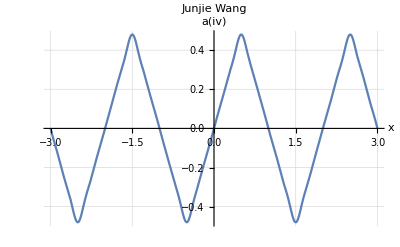

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

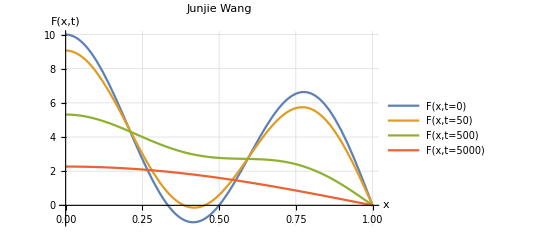

```mathematica
L = 1;
F[x_]:= {Piecewise[{{x,0<x<L/2},{1-x,L/2<x<L}}]}
F1[x_]:= {Piecewise[{{x,-L/2<x<0},{-1-x,-L<x<-L/2}}]}
F2[x_]:=If [x>0,F[x],F1[x]];
Range[F2[x]]={-L,L};

B[n_]=Simplify[2/L ∫_0^L F2[x]*Sin[n*Pi*x/L]ⅆx,Assumptions-> n∈Integers]
```